## Initialisations

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Needs["PlotLegends`"];*)
```

```mathematica
mt=173.2;
mb=4.2;
mW=80.385;
mZ=91.1876;
mh=125;
αEM=1/127.9;
αS=0.1184;
e=Sqrt[4 π αEM];
sw2=0.2312;
sw=Sqrt[sw2];
cw=Sqrt[1-sw2];
tw=sw/cw;
gW=e/sw;
gZ=gW/cw;
v=2 mW sw/e;
```

0.651892

0.74348

246.621

```mathematica
Nc=3;
Qt=2/3;
Qb=-1/3;
```

## Common block

mixing angles

```mathematica
tan2θL[m11_,m12_,m21_,m22_]:=-2(m11 m21+m22 m12)/((m11^2+m12^2)-(m22^2+m21^2))
tan2θR[m11_,m12_,m21_,m22_]:=-2(m11 m12+m22 m21)/((m11^2+m21^2)-(m22^2+m12^2))
sθL[m11_,m12_,m21_,m22_]:=Sin[ArcTan[tan2θL[m11,m12,m21,m22]]/2]
sθR[m11_,m12_,m21_,m22_]:=Sin[ArcTan[tan2θR[m11,m12,m21,m22]]/2]
cθL[m11_,m12_,m21_,m22_]:=Cos[ArcTan[tan2θL[m11,m12,m21,m22]]/2]
cθR[m11_,m12_,m21_,m22_]:=Cos[ArcTan[tan2θR[m11,m12,m21,m22]]/2]
```

mass eigen values

```mathematica
mq1[m11_,m12_,m21_,m22_]:=(1/Sqrt[2])Sqrt[(m11^2+m12^2+m21^2+m22^2)-Sqrt[(m11^2+m12^2+m21^2+m22^2)^2-4(m11 m22-m12 m21)^2]]
mq2[m11_,m12_,m21_,m22_]:=(1/Sqrt[2])Sqrt[(m11^2+m12^2+m21^2+m22^2)+Sqrt[(m11^2+m12^2+m21^2+m22^2)^2-4(m11 m22-m12 m21)^2]]
```

mass ratios

```mathematica
xqt[m11_,m12_,m21_,m22_]:=mt/mq2[m11,m12,m21,m22]
xqb[m11_,m12_,m21_,m22_]:=mb/mq2[m11,m12,m21,m22]
xqW[m11_,m12_,m21_,m22_]:=mW/mq2[m11,m12,m21,m22]
xqZ[m11_,m12_,m21_,m22_]:=mZ/mq2[m11,m12,m21,m22]
xqh[m11_,m12_,m21_,m22_]:=mh/mq2[m11,m12,m21,m22]
xqϕ[mϕ_,m11_,m12_,m21_,m22_]:=mϕ/mq2[m11,m12,m21,m22]
```

phase space function

```mathematica
λ[x_,y_]:=1+x^2+y^2-2 x-2 y-2 x y
```

loop functions

```mathematica
ηp[τ_]:=1+Sqrt[1-τ]
ηm[τ_]:=1-Sqrt[1-τ]
f[τ_]:=HeavisideTheta[τ-1](ArcSin[1/Sqrt[τ]])^2-HeavisideTheta[1-τ](1/4)(Log[ηp[τ]/ηm[τ]]-I π)^2
f12ϕ[τ_]:=-2τ(1+(1-τ) f[τ])
f12η[τ_]:=-2τ f[τ]
g[τ_]:=HeavisideTheta[τ-1](Sqrt[τ-1])(ArcSin[1/Sqrt[τ]]) +
HeavisideTheta[1-τ] (Sqrt[1-τ]/2)(Log[(1+Sqrt[1-τ])/(1-Sqrt[1 - τ]) - I π])
Iphi[τ_,λ_] := ((τ λ)/(2(τ-λ))) + (((τ^2 λ^2+τ λ(τ - λ))/(2(τ-λ)^2))(f[τ]-f[λ]))+ ((τ^2 λ)/(τ - λ)^2)(g[τ]-g[λ])
IEta[τ_,λ_]:= ((τ λ)/(2 (τ-λ)))(f[τ]-f[λ])
```

#### Limit from γγ data

```mathematica
MXCSobs=Import["exclusion_data/MS_CS_ATLAS_observed_2102-13405.dat",{"Data",{All},{1,2}}];
FFMXCSobs=Interpolation[MXCSobs];
MXCE=Import["exclusion_data/A_ggF_139.dat",{"Data",{All},{1,2}}];
FFMXCE=Interpolation[MXCE];
Mϕσ=Import["exclusion_data/mphi_CS_gg2phi_k0_01.dat",{"Data",{All},{1,2}}];
FFMϕσ=Interpolation[Mϕσ];
σϕLO=Import["exclusion_data/mass_cs_phi.dat",{"Data",{All},{1,2}}];
FFσϕLO=Interpolation[σϕLO];
σϕNNLO=Import["exclusion_data/mass_cs_phi.dat",{"Data",{All},{1,4}}];
FFσϕNNLO=Interpolation[σϕNNLO];
```

#### Limit from T searches

```mathematica
TpSD=Import["exclusion_data/tPhi_lims_singlet.txt",{"Data",{All},{2,1}}];
FTpSDlim=Interpolation[TpSD];
```

## Singlet T

### Free Parameters

```mathematica
λaϕ=0.5698625928946173;
λbϕ=0.23734578606956713;
mt12=10.995556922229873;
mt21=0.0;
```

```mathematica
mϕ=700;
mt11=mt;
mt22=1200;
```

### Check Mixing angles, Mass Eigenvalues

```mathematica
sθL[mt11,mt12,mt21,mt22]
```

0.00241463

```mathematica
sθR[mt11,mt12,mt21,mt22]
```

0.000296024

```mathematica
cθL[mt11,mt12,mt21,mt22]
```

0.999998

```mathematica
cθR[mt11,mt12,mt21,mt22]
```

1.

```mathematica
mq1[mt11,mt12,mt21,mt22]
```

173.195

```mathematica
mq2[mt11,mt12,mt21,mt22]
```

1200.03

New Physics coupling   from [arxiv:1305.4172], eq. 2.20

```mathematica
κTL[sθL_,cθL_, sθR_,cθR_, mVLQ_] := sθL^2 + (cθL*sθL)^2*0.5 +((mt/v)*cθL*sθR + (mt12/v)*cθL*cθR)^2*(0.5 - (mh/mVLQ)^2)
```

```mathematica
κTL[sθL[mt11,mt12,mt21,mt22],cθL[mt11,mt12,mt21,mt22],sθR[mt11,mt12,mt21,mt22],cθR[mt11,mt12,mt21,mt22], 1200]
```

0.0000745043

## t_2 decay

### t_2→bW decay width

```mathematica
kt2LbLW[m11_,m12_,m21_,m22_]:=gW sθL[m11,m12,m21,m22]/Sqrt[2]
kt2RbRW[m11_,m12_,m21_,m22_]:=0
Γt2bW[m11_,m12_,m21_,m22_]:=Which[mq2[m11,m12,m21,m22]>mb+mW,(1/(32 π)) (mq2[m11,m12,m21,m22]^3/mW^2) ((kt2LbLW[m11,m12,m21,m22]^2+kt2RbRW[m11,m12,m21,m22]^2) ((1-xqb[m11,m12,m21,m22]^2)^2+xqW[m11,m12,m21,m22]^2(1+xqb[m11,m12,m21,m22]^2)-2 xqW[m11,m12,m21,m22]^4)-12 kt2LbLW[m11,m12,m21,m22] kt2RbRW[m11,m12,m21,m22] xqb[m11,m12,m21,m22] xqW[m11,m12,m21,m22]^2) Sqrt[λ[xqb[m11,m12,m21,m22]^2,xqW[m11,m12,m21,m22]^2]],mq2[m11,m12,m21,m22]<mb+mW,0]
```

### t_2→tZ decay width

```mathematica
kt2Lt1LZ[m11_,m12_,m21_,m22_]:=(gZ/2) cθL[m11,m12,m21,m22] sθL[m11,m12,m21,m22]
kt2Rt1RZ[m11_,m12_,m21_,m22_]:=0
Γt2tZ[m11_,m12_,m21_,m22_]:=Which[mq2[m11,m12,m21,m22]>mq1[m11,m12,m21,m22]+mZ,(1/(32 π)) (mq2[m11,m12,m21,m22]^3/mZ^2) ((kt2Lt1LZ[m11,m12,m21,m22]^2+kt2Rt1RZ[m11,m12,m21,m22]^2) ((1-xqt[m11,m12,m21,m22]^2)^2+xqZ[m11,m12,m21,m22]^2 (1+xqt[m11,m12,m21,m22]^2)-2 xqZ[m11,m12,m21,m22]^4)-12 kt2Lt1LZ[m11,m12,m21,m22] kt2Rt1RZ[m11,m12,m21,m22] xqt[m11,m12,m21,m22] xqZ[m11,m12,m21,m22]^2) Sqrt[λ[xqt[m11,m12,m21,m22]^2,xqZ[m11,m12,m21,m22]^2]],mq2[m11,m12,m21,m22]<mq1[m11,m12,m21,m22]+mZ,0]
```

### t_2→th decay width

```mathematica
kt1Lt2Rh[m11_,m12_,m21_,m22_]:=(m11 cθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22]+m12 cθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22])/v
kt1Rt2Lh[m11_,m12_,m21_,m22_]:=(m11 sθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22]-m12 sθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22])/v
Γt2th[m11_,m12_,m21_,m22_]:=Which[mq2[m11,m12,m21,m22]>mq1[m11,m12,m21,m22]+mh,(1/(32 π)) mq2[m11,m12,m21,m22] ((kt1Lt2Rh[m11,m12,m21,m22]^2+kt1Rt2Lh[m11,m12,m21,m22]^2) (1+xqt[m11,m12,m21,m22]^2-xqh[m11,m12,m21,m22]^2)+4 kt1Lt2Rh[m11,m12,m21,m22]kt1Rt2Lh[m11,m12,m21,m22] xqt[m11,m12,m21,m22]) Sqrt[λ[xqt[m11,m12,m21,m22]^2,xqh[m11,m12,m21,m22]^2]],mq2[m11,m12,m21,m22]<mq1[m11,m12,m21,m22]+mh,0]
```

### t_2→tϕ decay width

```mathematica
kt1Lt2Rϕ[m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=-λaϕ sθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22]-λbϕ sθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22]
kt1Rt2Lϕ[m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=-λaϕ cθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22]+λbϕ cθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22]
Γt2tϕ[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Which[mq2[m11,m12,m21,m22]>mq1[m11,m12,m21,m22]+mϕ,(1/(32 π)) mq2[m11,m12,m21,m22] ((kt1Lt2Rϕ[m11,m12,m21,m22,λaϕ,λbϕ]^2+kt1Rt2Lϕ[m11,m12,m21,m22,λaϕ,λbϕ]^2) (1+xqt[m11,m12,m21,m22]^2-xqϕ[mϕ,m11,m12,m21,m22]^2)+4 kt1Lt2Rϕ[m11,m12,m21,m22,λaϕ,λbϕ]kt1Rt2Lϕ[m11,m12,m21,m22,λaϕ,λbϕ] xqt[m11,m12,m21,m22]) Sqrt[λ[xqt[m11,m12,m21,m22]^2,xqϕ[mϕ,m11,m12,m21,m22]^2]],mq2[m11,m12,m21,m22]<mq1[m11,m12,m21,m22]+mϕ,0]
```

### Decay Width, Branching Ratios.

```mathematica
Γt2[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γt2bW[m11,m12,m21,m22]+Γt2tZ[m11,m12,m21,m22]+Γt2th[m11,m12,m21,m22]+Γt2tϕ[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRt2bW[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γt2bW[m11,m12,m21,m22]/Γt2[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRt2tZ[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γt2tZ[m11,m12,m21,m22]/Γt2[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRt2th[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γt2th[m11,m12,m21,m22]/Γt2[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRt2tϕ[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γt2tϕ[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]/Γt2[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
```

#### Branching Ratio plot for t_2 (set free parameters above)

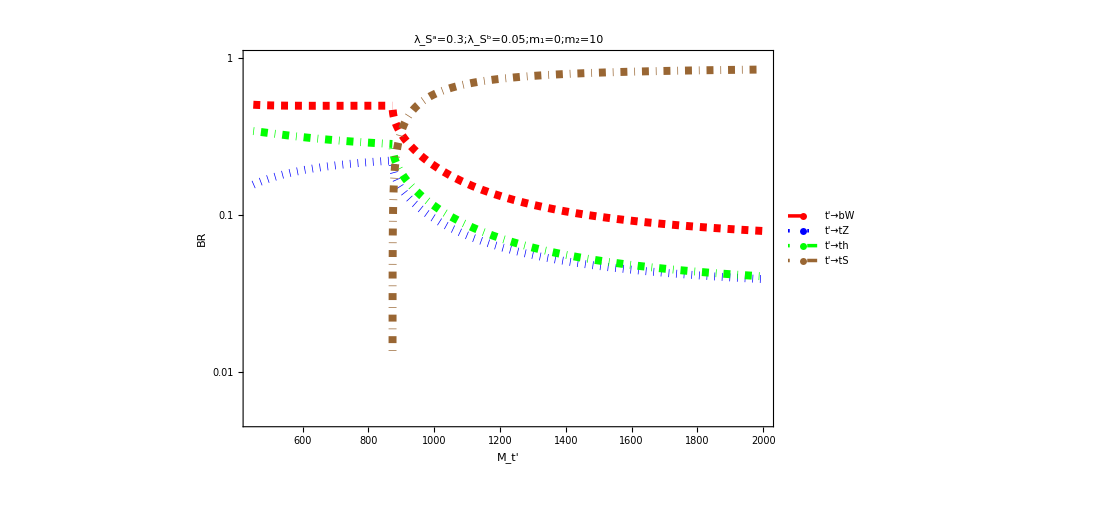

```mathematica
LogPlot[{BRt2bW[mϕ,mt11,mt12,mt21,m22,λaϕ,λbϕ],BRt2tZ[mϕ,mt11,mt12,mt21,m22,λaϕ,λbϕ],BRt2th[mϕ,mt11,mt12,mt21,m22,λaϕ,λbϕ],BRt2tϕ[mϕ,mt11,mt12,mt21,m22,λaϕ,λbϕ]},{m22,450,2000},Frame->True,FrameStyle->Thick,PlotRange->{{450,2000},{0.005,1}},PlotStyle->{{Red,Dashed,Thickness[0.007]},{Blue,Dotted,Thickness[0.007]},{Green,DotDashed,Thickness[0.007]},{Brown,DotDashed,Thickness[0.007]}},PlotLegends->Placed[LineLegend[Automatic,{Style["t'→bW",15],Style["t'→tZ",15],Style["t'→th",15],Style["t'→tϕ",15]},LegendMarkers->Graphics[{Thickness[0.14],Line[{{-10,0},{10,0}}]}],LegendMarkerSize->20],{0.9,0.8}],FrameLabel->{"M_t_2","BR"},LabelStyle->FontSize->20]
```

```mathematica
paralist90={};
n=0;
While[n<1001,AppendTo[paralist90,{N[400+n*1.6], BRt2bW[mϕ,mt11,mt12,mt21,N[400+n*1.6],λaϕ,λbϕ],BRt2tZ[mϕ,mt11,mt12,mt21,N[400+n*1.6],λaϕ,λbϕ],BRt2th[mϕ,mt11,mt12,mt21,N[400+n*1.6],λaϕ,λbϕ],BRt2tϕ[mϕ,mt11,mt12,mt21,N[400+n*1.6],λaϕ,λbϕ]}];n++]
Export["BR_SingT1200Phi700_t2decay.dat",paralist90];
Remove[paralist90];PRD_ColliderPaper_bMarks
```

## ϕ decay

```mathematica
kt1Lt1Rϕ[m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=λaϕ sθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22]-λbϕ sθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22]
kt2Lt2Rϕ[m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=λaϕ cθL[m11,m12,m21,m22] cθR[m11,m12,m21,m22]+λbϕ cθL[m11,m12,m21,m22] sθR[m11,m12,m21,m22]
```

### ϕ → γγ

```mathematica
Γϕγγt[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=(αEM^2/(256 π^3)) (mϕ^3)Nc^2(Qt)^4 (Abs[kt1Lt1Rϕ[m11,m12,m21,m22,λaϕ,λbϕ] f12ϕ[4(mq1[m11,m12,m21,m22])^2/mϕ^2]/mq1[m11,m12,m21,m22]+kt2Lt2Rϕ[m11,m12,m21,m22,λaϕ,λbϕ] f12ϕ[4(mq2[m11,m12,m21,m22])^2/mϕ^2]/mq2[m11,m12,m21,m22]])^2
```

### ϕ → gg

```mathematica
Γϕggt[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=(αS^2/(128 π^3)) (mϕ^3)(Abs[kt1Lt1Rϕ[m11,m12,m21,m22,λaϕ,λbϕ] f12ϕ[4(mq1[m11,m12,m21,m22])^2/mϕ^2]/mq1[m11,m12,m21,m22]+kt2Lt2Rϕ[m11,m12,m21,m22,λaϕ,λbϕ] f12ϕ[4(mq2[m11,m12,m21,m22])^2/mϕ^2]/mq2[m11,m12,m21,m22]])^2
```

### ϕ → tt

```mathematica
Γϕtt[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Which[mϕ>2mq1[m11,m12,m21,m22],(3/(8π))(kt1Lt1Rϕ[m11,m12,m21,m22,λaϕ,λbϕ])^2 mϕ(1-4(mq1[m11,m12,m21,m22])^2/mϕ^2)^(3/2),mϕ<2mq1[m11,m12,m21,m22],0]
```

### ϕ → Zγ

```mathematica
ΓϕZγt[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:= ((αEM^2 mϕ^3 Nc^2 Qt^2)/(32 π^3 sw2 cw^2))(1 - mZ^2/mϕ^2)^3(Abs[1/mt kt1Lt1Rϕ[m11,m12,m21,m22,λaϕ,λbϕ] (0.5 (cθL[m11,m12,m21,m22])^2- 2 Qt sw2)  Iphi[(4(mq1[mt11,mt12,mt21,mt22])^2)/mϕ^2,(4(mq1[mt11,mt12,mt21,mt22])^2)/mZ^2]+ 1/mt22 kt2Lt2Rϕ[m11,m12,m21,m22,λaϕ,λbϕ](0.5 (sθL[m11,m12,m21,m22])^2- 2 Qt sw2 )Iphi[(4(mq2[mt11,mt12,mt21,mt22])^2)/mϕ^2,(4(mq2[mt11,mt12,mt21,mt22])^2)/mZ^2] ])^2
```

### Decay Width, Branching Ratios

```mathematica
Γϕt[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γϕggt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]+Γϕγγt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]+Γϕtt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ] + ΓϕZγt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRϕγγt[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γϕγγt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]/Γϕt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRϕggt[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γϕggt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]/Γϕt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRϕtt[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:=Γϕtt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]/Γϕt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
BRϕZγt[mϕ_,m11_,m12_,m21_,m22_,λaϕ_,λbϕ_]:= ΓϕZγt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]/Γϕt[mϕ,m11,m12,m21,m22,λaϕ,λbϕ]
```

### Branching Ratio plot for ϕ (set Free Parameters above)

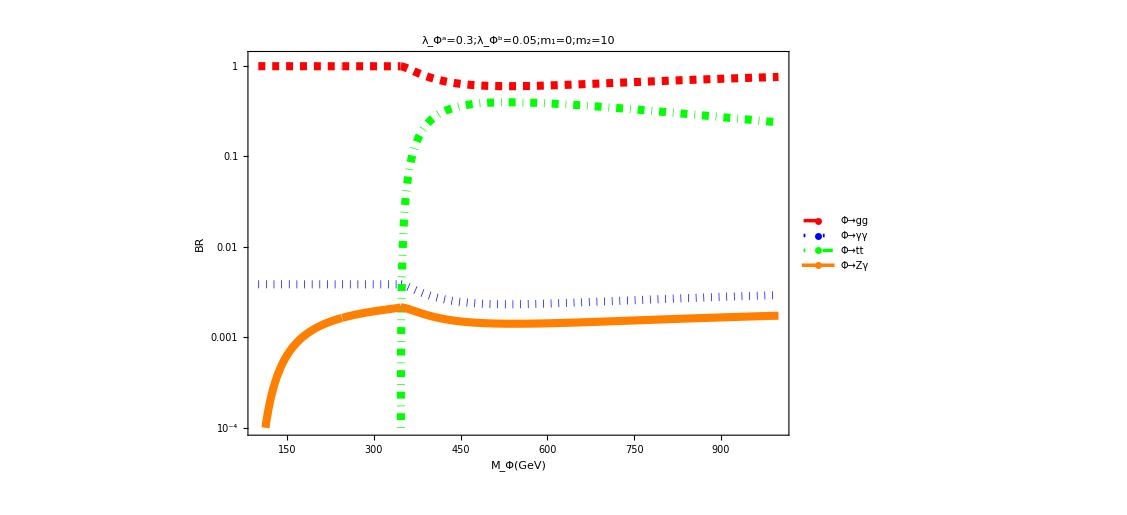

```mathematica
LogPlot[{BRϕggt[mϕ,mt11,mt12,mt21,mt22,λaϕ,λbϕ],BRϕγγt[mϕ,mt11,mt12,mt21,mt22,λaϕ,λbϕ],BRϕtt[mϕ,mt11,mt12,mt21,mt22,λaϕ,λbϕ],BRϕZγt[mϕ,mt11,mt12,mt21,mt22,λaϕ,λbϕ]},{mϕ,100,1000},Frame->True,FrameStyle->Thick,PlotRange->{{100,1000},{0.0001,1.2}},PlotStyle->{{Red,Dashed,Thickness[0.007]},{Blue,Dotted,Thickness[0.007]},{Green,DotDashed,Thickness[0.007]},{Orange, Thickness[0.007]}},PlotLegends->Placed[LineLegend[Automatic,{Style["Φ→gg",15],Style["Φ→γγ",15],Style["Φ→tt",15], Style["Φ→Zγ",15]},LegendMarkers->Graphics[{Thickness[0.14],Line[{{-10,0},{10,0}}]}],LegendMarkerSize->20],{0.9,0.8}],FrameLabel->{Subscript[M,ϕ][GeV],BR},LabelStyle->FontSize->20]
```

```mathematica
paralist80={};
n=0;
While[n<1001,AppendTo[paralist80,{N[100+n*0.9], BRϕggt[N[100+n*0.9],mt11,mt12,mt21,mt22,λaϕ,λbϕ],BRϕγγt[N[100+n*0.9],mt11,mt12,mt21,mt22,λaϕ,λbϕ],BRϕtt[N[100+n*0.9],mt11,mt12,mt21,mt22,λaϕ,λbϕ], BRϕZγt[N[100+n*0.9],mt11,mt12,mt21,mt22,λaϕ,λbϕ]}];n++]
Export["PRD_ColliderPaper_bMarks/BR_SingT1200Phi700_PhiDecay.dat",paralist80];
Remove[paralist80];
```

## Parameter Scan

```mathematica
mϕL=350;
mt11L=mt;
mt22L=1300;
```

```mathematica
LLBR = 0.7;
TLBR = 0.0;
```

```mathematica
n=0;
npts =40000;
paralistColor={};
Rm12:=RandomReal[{0,50}];
m21=0;
Rλa:=RandomReal[{0.0,1.0}];
Rλb:=RandomReal[{0.0,1.0}];
While[n<npts,{m12,λa,λb}={Rm12,Rλa,Rλb};If[BRt2tϕ[mϕL,mt11L,m12,m21,mt22L,λa,λb]> FTpSDlim[mq2[mt11L,m12,m21,mt22L]/1000]&& ((kt1Lt1Rϕ[mt11L,m12,m21,mt22L,λa,λb]+kt2Lt2Rϕ[mt11L,m12,m21,mt22L,λa,λb])^2/0.01^2/48^2/π^4) (FFσϕNNLO[mϕL]/FFσϕLO[mϕL]) FFMϕσ[mϕL] FFMXCE[mϕL]BRϕγγt[mϕL,mt11L,m12,m21,mt22L,λa,λb] 1000<FFMXCSobs[mϕL],
If[BRϕggt[mϕL,mt11L,m12,m21,mt22L,λa,λb]>LLBR,AppendTo[paralistColor,{m12,m21,λa,λb}]]];n++]
Export["Scans/SingT/BR_Phi2GG_gt0.5"<>ToString[LLBR]<>"_mTp_"<>ToString[mt22L]<>"_mS_"<>ToString[mϕL]<>"_"<>ToString[IntegerPart[npts/1000]]<>"K.dat",paralistColor];
Remove[paralistColor];
```